# Cross Mode

#### Animation of the cross polarization mode of gravitational waves in f(R) theories. The notebook generates the corresponding deformation patterns of a ring of test particles and associated animation via the geodesic deviation equation.

```mathematica
$Assumptions ={x ∈ Reals, y ∈ Reals, z ∈ Reals, t ∈ Reals, ω ∈ Reals}
```

{x∈ℝ,y∈ℝ,z∈ℝ,t∈ℝ,ω∈ℝ}

```mathematica
n=4; var= {x,y,z,t};k={0,0,ω,ω};
```

```mathematica
Do[η[i,j] = If[i == j, 1, 0],{i,1,n},{j,1,n}]; η[4,4] = -1; eta = Table[η[i,j],{i,1,n},{j,1,n}];
```

```mathematica
ηm=Table[η[i,j],{i,1,n},{j,1,n}];ηma=MatrixForm[ηm]; Print[Style["η_μν = ", 18], Style[ηma, 18]];
```

η_μν = (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

```mathematica
S1[z_,t_] = S10 + 1/2 hc  Sin[Sum[η[i,j] k[[i]] var[[j]],{i,1,4},{j,1,4}]]S20
```

S10-1/2 hc S20 Sin[t ω-z ω]

```mathematica
S2[z_,t_] = S20 + 1/2 hc  Sin[Sum[η[i,j] k[[i]] var[[j]],{i,1,4},{j,1,4}]] S10
```

S20-1/2 hc S10 Sin[t ω-z ω]

```mathematica
values2={hc->1,S10-> 1,S20->2,ω->1}
```

{hc→1,S10→1,S20→2,ω→1}

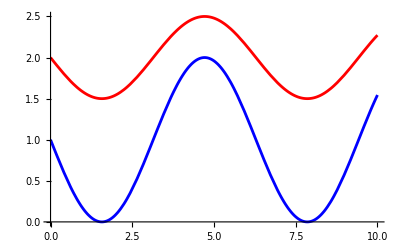

```mathematica
Plot[{S1[0,t]/.values2 ,S2[0,t]/.values2 },{t,0,10}, PlotStyle->{Blue,Red},PlotRange->Automatic]
```

```mathematica
values1={hc->1,ω->1}
```

{hc→1,ω→1}

```mathematica
solgen=  Extract[Solve[{S1[0,0]== Cos[θ], S2[0,0] == Sin[θ]},{S10,S20}],1]
```

{S10→Cos[θ],S20→Sin[θ]}

```mathematica
Animator[Dynamic[tfin],{0,20}, AnimationRate->1, AnimationRunning->False,AppearanceElements->All]
```

```mathematica
Dynamic[ParametricPlot[{S1[0,tfin]/. solgen /. values1,S2[0,tfin]/.solgen/.values1},{θ,0,2π},PlotRangePadding-> 1,PlotRange->{{-1,1},{-1,1}},Axes->True,AxesLabel->{S1, S2}, GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed], PlotStyle->Purple]]
```

#### Download GIF

```mathematica
frames=Table[ParametricPlot[{S1[0,t]/. solgen/. values1,S2[0,t]/. solgen/. values1},{θ,0,2 π},PlotRange->{{-1,1},{-1,1}},PlotRangePadding->1,PlotRange->{{-1,1},{-1,1}},Axes->True,AxesLabel->{S1, S2}, GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],PlotStyle->Purple, PlotLabel->Style["Cross Mode "<>ToString[NumberForm[t,{3,2}]],14,Bold,Black],ImageSize->400],{t,0,10,0.1}  (*aquí defines el rango y paso de tfin*)];
Export["C:\\Users\\cindy\\OneDrive\\Escritorio\\Tesis\\Código\\Gifs_Polarizaciones/crossmode.gif",frames,"GIF"]
```

C:\Users\cindy\OneDrive\Escritorio\Tesis\Código\Gifs_Polarizaciones/crossmode.gif

```mathematica
Do[points[θ][t_]= {S1[0,t]/. solgen /. values1,S2[0,t]/.solgen/.values1},{θ,0,2π,π/4}];
```

#### Dots Animation

```mathematica
Animator[Dynamic[tfin],{0,20}, AnimationRate->1, AnimationRunning->False,AppearanceElements->All]
```

```mathematica
Dynamic[Show[Graphics[{PointSize[Medium],Black,Point[{0,0}]},PlotRangePadding-> 1,PlotRange->{{-2,2},{-2,2}}],Table[Graphics[{PointSize[Large],Purple,Point[points[θ][tfin]]}],{θ,0,2π,π/4}], Axes->True,AxesLabel->{"S1","S2"}]]
```

#### GIF Download

```mathematica
dt=0.1;

(*Generar frames de la animación*)
frames=Table[Show[Graphics[{PointSize[Medium],Black,Point[{0,0}]},PlotRangePadding->1,PlotRange->{{-2,2},{-2,2}}],Table[Graphics[{PointSize[Large],Purple,Point[points[θ][t]]}],{θ,0,2 Pi,Pi/4}],Axes->True,AxesLabel->{"S1","S2"},ImageSize->400],{t,0,tmax,dt}];

(*Exportar como GIF*)
Export["\\Users\\cindy\\OneDrive/Desktop/cross_dots.gif",frames,"GIF"]
```

Table::iterb: Iterator {t,0,tmax,0.1} does not have appropriate bounds.

\Users\cindy\OneDrive/Desktop/cross_dots.gif

```mathematica
(□_□)_□
```

(□_□)_□